In this notebook is simulated the Activator-Inhibitor system regulation with GA and the three-stage model (burst expression). The notebook has two parts:
1. To evaluate the “sensitivity” to the whole set the parameters. With an arbitrary start point to calculate the estimates (FF, CV2,Mean) (30% of the total number of iterations), and different number of iterations to get a final t of 1500. 
2. To evaluate 4 specific regions or set of parameters

## Parameters for the two sessions

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
name=0.5; (* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,name,0.02]; (* subRanges: 0.02-0.5, 0.52-1.0, 1.02-1.5, 1.52-2 *)
γms=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
γps=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
parametro="γg";(* With the name of the second parameter is named the output file *)
```

These are the default values of parameters

```mathematica
{kgA,kgI}={0.01158,0.01158};(* Gene activation rate (t^-1)*)
{γgA,γgI}= {2.082,2.082};(* Gene desactivation rate (t^-1) *)
{kmA,kmI}={0.696,0.696};(* Production rate of mRNA (molecules*t^-1) *)
{γmA,γmI}={0.02082  ,0.02082 };(* mRNA Degradation rate (molecules*t^-1) *)
{kpA,kpI}={1.386,1.386};(* protein Production (molecules*t^-1) *)
{γpA,γpI}={0.02082  ,0.02082 }(* protein Degradation rate (molecules*t^-1) *)
h=3 (* Hill's constant *);
kIA=kAA=kAI=100;(* Michaeles-Menten Constant *)

{bmA,bmI}={kmA/(γgA+kgA),kmI/(γgI+kgI)};(* Burst size mean (molecules-mRNA) *)
{bpA,bpI}={kpA/γmA,kpI/γmI};(* Burst size mean (molecules-proteins) *)
kaa=γg/kg(* Michaeles-Menten Constant of regulation of a by a *);
kia=γg/kg(* Michaeles-Menten Constant of regulation of a by i *);
kai=γg/kg(* Michaeles-Menten Constant of regulation of i by a *);
kat=γg/kg(* Michaeles-Menten Constant of regulation of t by a *);
```

## Functions for the two sessions

These are the reactions (changesByRXN) and propensity functions (pF) of the GA for the specific regulation system: A: Activator -> I : Inhibitor gene

```mathematica
changesByRXN=Function/@<|1->{#1,#2,#3,#4,#5-1,#6+1,#7,#8},2->{#1,#2,#3,#4,#5+1,#6-1,#7,#8},3->{#1+1,#2,#3,#4,#5,#6,#7,#8},4->{#1,#2+1,#3,#4,#5,#6,#7,#8},5->{#1-1,#2,#3,#4,#5,#6,#7,#8},6->{#1,#2-1,#3,#4,#5,#6,#7,#8},7->{#1,#2,#3,#4,#5,#6,#7-1,#8+1},8->{#1,#2,#3,#4,#5,#6,#7+1,#8-1},9->{#1,#2,#3+1,#4,#5,#6,#7,#8},10->{#1,#2,#3,#4+1,#5,#6,#7,#8},11->{#1,#2,#3-1,#4,#5,#6,#7,#8},12->{#1,#2,#3,#4-1,#5,#6,#7,#8}|>;(* Each hash represents a specie: mRNAA-proteinA-mRNAB-proteinB-da0A:promoterInactivatedA-da1A:promoterActivatedA-db0B-db1B
   The numbers are the next reactions: 1-7-> Activation, 2-8-> Desactivation, 3-4-9-10-> Synthesis, 5-6-11-12-> Degradation*)

pF=Compile[{{h,_Real},{kIA,_Real},{kAA,_Real},{kAI,_Real},{kgA,_Real},{γgA,_Real},{kmA,_Real},{γmA,_Real},{kpA,_Real},{γpA,_Real},{kgI,_Real},{γgI,_Real},{kmI,_Real},{γmI,_Real},{kpI,_Real},{γpI,_Real},{mRNAA,_Integer},{proteinA,_Integer},{mRNAI,_Integer},{proteinI,_Integer},{d0A,_Integer},{d1A,_Integer},{d0I,_Integer},{d1I,_Integer}},{d0A*kgA*(1/(1+(proteinI/kIA)^h))(proteinA^h/(kAA+proteinA^h))(*La inhibición de I hacia A esta aqui*),d1A*γgA,d1A*kmA+0.01,kpA*mRNAA,mRNAA*γmA,γpA*proteinA,d0I*kgI*(proteinA^h/(kAI+proteinA^h)),d1I*γgI,d1I*kmI+0.01,kpI*mRNAI,mRNAI*γmI,γpI*proteinI},RuntimeAttributes->{Listable},Parallelization->True];
```

This is equal for all  sub-circuits

```mathematica
ff[dato_]:=N[Variance[dato]/Mean[dato]];(* Fano Factor for noise measure *)
expressionNoise[data_]:=N[Variance[data]/Mean[data]^2](* Squared Coefficient of Variation for noise measure *)
```

```mathematica
(* This is the algorithm to estimate the Steady State start from Kelly and Hedengren 2013 *)
steadyStateStart[window_,listData_]:=Block[{n,dataByWindow,mPorVentana,μ,sd,probabilidades},
n=Floor[Length[#]/window]&[listData];
dataByWindow=Partition[#,n]&[listData[[All,2]]];mPorVentana=Map[Mean[#[[2;;All]]-#[[1;;-2]]]&,dataByWindow];μ=MapThread[(1/n)(Total[#1]-#2*Total[Range[1,n](*tPorVentana*)])&,{dataByWindow,mPorVentana}];sd=Table[Sqrt[(1/(n-2))*Sum[(dataByWindow[[i,j]]-mPorVentana[[i]]*j-μ[[i]])^2,{j,1,Length[dataByWindow[[i]]]}]],{i,window}];probabilidades=Map[Total[#]/n&,Table[If[Abs[dataByWindow[[i,j]]-μ[[i]]]≤sd[[i]],1,0],{i,window},{j,1,n}]]//N;
((Position[probabilidades,x_/;x>0.1][[1,1]]-1)*n)+1]
```

## S1: All range parameters values

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=5; (* Number of times the algorithm is run *)
```

### Simulation

```mathematica
(* Launch the number of kernels in which you will parallelize the simulation *)
LaunchKernels[44]
```

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
DistributeDefinitions[changesByRXN,pF,ff,expressionNoise,iteraciones,h,kIA,kAA,kAI,kgA,γgA,kmA,γmA,kpA,γpA,kgI,γgI,kmI,γmI,kpI,γpI];
(*List by parameters*)
mRNAffcv2ListA={};
proteinffcv2ListA={};
mRNAffcv2ListI={};
proteinffcv2ListI={};

Do[
(*List by replicates*)
listEstimatemRNAA={};
listEstimateproteinA={};
listEstimatemRNAI={};
listEstimateproteinI={};
 listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI, listDataAndTimeT];

ParallelDo[

listDataAndTime = CreateDataStructure["OrderedHashSet"];
abundancia={1,1,1,1,1,0,1,0}(*mRNAA,proteinA,mRNAI,proteinI,da0A,da1A,db0I,db1I*);
t=0;

Do[
τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[h,kIA,kAA,kAI,kgA,γgA,kmA,γmA,kpA,γpA,kgI,γgI,kmI,γmI,kpI,γpI,Sequence@@abundancia]];
reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];         
 listDataAndTime["Union", {{t, abundancia}}];
            If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones1 ];

  listData = Normal[listDataAndTime][[All, 2]];
        ini =Echo@Round[(Length[listData]*30)/100.] (*el estado estable se considera depués del 30% de iteraciones *);
(*ini = steadyStateStart[window,listData];*)
{mRNAffcv2ItA,proteinffcv2ItA}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];
{mRNAffcv2ItI,proteinffcv2ItI}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]},{i,{listData[[ini;;All,3]],
listData[[ini;;All,4]]}}];

AppendTo[listEstimatemRNAA,mRNAffcv2ItA];
AppendTo[listEstimateproteinA,proteinffcv2ItA];
AppendTo[listEstimatemRNAI,mRNAffcv2ItI];
AppendTo[listEstimateproteinI,proteinffcv2ItI];
AppendTo[listDataAndTimeT,listDataAndTime];,


replicas1];

AppendTo[mRNAffcv2ListA,Mean[listEstimatemRNAA]];
AppendTo[proteinffcv2ListA,Mean[listEstimateproteinA]];
AppendTo[mRNAffcv2ListI,Mean[listEstimatemRNAI]];
AppendTo[proteinffcv2ListI,Mean[listEstimateproteinI]];,

    
 {kg,{1}},{γg,{0.01}}]; (*CAMBIAR AQUI EN EL .m*)
```

>> 4172

>> 5132

>> 5294

>> 6386

```mathematica
(* CAMBIAR AQUI EN EL .m _Cuando cambiamos A *****************)
```

```mathematica
Export["controlAIGAA_A"<>parametro<>ToString[name],{mRNAffcv2ListA,proteinffcv2ListA},"CSV"];
Export["controlAIGAA_I"<>parametro<>ToString[name],{mRNAffcv2ListI,proteinffcv2ListI},"CSV"];
```

```mathematica
(* CAMBIAR AQUI EN EL .m _Cuando cambiamos I *****************)
```

```mathematica
Export["controlAIGAI_A"<>parametro<>ToString[name],{mRNAffcv2ListA,proteinffcv2ListA},"CSV"];
Export["controlAIGAI_I"<>parametro<>ToString[name],{mRNAffcv2ListI,proteinffcv2ListI},"CSV"];
```

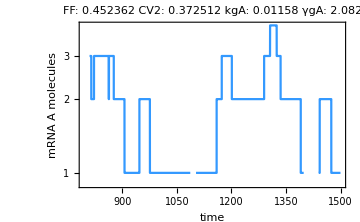
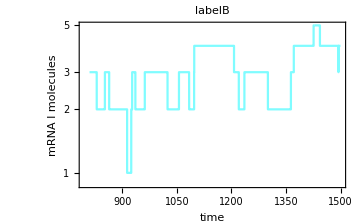
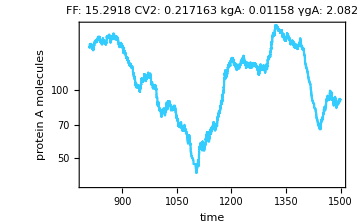
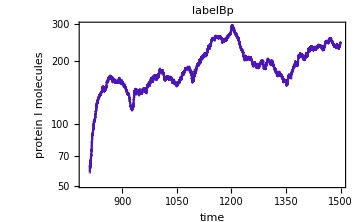
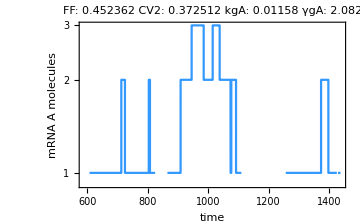
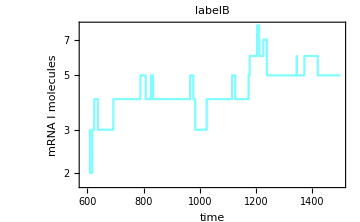
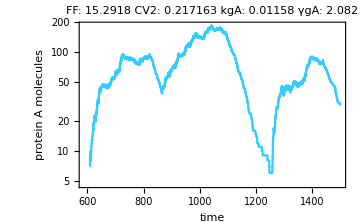
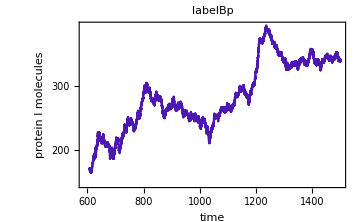

```mathematica
listDataAndTimeTN=Normal/@listDataAndTimeT;
MapThread[plotsLogExpression[#1,#2,listDataAndTimeTN,"","","","",""]&,{Range[1,replicas1],{3864,5708,5625,6087}}]
```

## S2: Evaluation by regions

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=500; (* Number of times the algorithm is run *)
rep=1; (* Some plots are made with the output of this replicate*)
lagStep=10; (* Lag time for the Autocorrelation plot *)
species=4;(*mRNA genA/B protein genA/B*)
```

### Functions

These functions make different plots of the temporal genes expression

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins *)plotsExpression[rep_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,mRNAffcv2MeanI_,proteinffcv2MeanI_,parametros_]:=Module[{datesListAm,datesListAp,datesListBm,datesListBp},
SetOptions[ListLinePlot,Frame-> True,ImageSize->Medium];

{datesListAm,datesListAp,datesListBm,datesListBp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,4}];{ListLinePlot[datesListAm,PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLinePlot[datesListBm,PlotStyle->
RGBColor[0.5,0.99,1],FrameLabel->{"time","mRNA I molecules"},PlotLabel->labelB],
ListLinePlot[datesListAp,PlotStyle->
RGBColor[0.2,.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp],
ListLinePlot[datesListBp,PlotStyle->
RGBColor[0.3,.09,0.7],FrameLabel->{"time","protein I molecules"},PlotLabel->labelBp]}]
```

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins with log scale *)plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,mRNAffcv2MeanI_,proteinffcv2MeanI_,parametros_]:=Module[{datesListAm,datesListAp,datesListBm,datesListBp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp,datesListBm,datesListBp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,4}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLogPlot[datesListBm[[ini;;]],PlotStyle->
RGBColor[0.5,0.99,1],FrameLabel->{"time","mRNA I molecules"},PlotLabel->labelB],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp],
ListLogPlot[datesListBp[[ini;;]],PlotStyle->
RGBColor[0.3,.09,0.7],FrameLabel->{"time","protein I molecules"},PlotLabel->labelBp]}]
```

```mathematica
(* This plots the auto-correlation of the temporal dynamic of genes mRNA and proteins *)
autoCorrPlot[lagStep_,listDataAndTimeTN_,positions_]:=Module[{data,lenght,data2,corr,negatives,cortes},
data=Table[MapThread[Extract[#1,#2]&,{listDataAndTimeTN[[All,All,2]][[All,All,i]],positions}],{i,{1,3,2,4}}];
lenght=Min[Length/@#]&/@data;
data2=MapThread[TemporalData[#1[[All,1;;#2]],{Range[1,#2]}]&,{data,lenght}](*This is to get the corr in each lag time as the average between replicates *);
DistributeDefinitions[data,data2];
corr=ParallelMap[CorrelationFunction[#,{1,#["PathLengths"][[1]]-1,lagStep}]&,data2];
negatives=FirstPosition[Normal[#],{_,_?Negative}]*lagStep&/@corr;
cortes=Count[Partition[#//Normal,2,1],{{_,_?Positive},{_,_?Negative}}|{{_,_?Negative},{_,_?Positive}}]&/@corr;
ListPlot[#[[1]],Filling->Axis ,Frame->True,ImageSize->Medium,FrameLabel->{"Lag-"<>ToString[lagStep],#[[2]]},PlotStyle->#[[4]],PlotLabel->"First negative: "<>ToString[#[[3]]]<>"\n cortes: "<>ToString[#[[5]]]]&/@{{corr[[1]],"mRNA A",negatives[[1]],RGBColor[0.2,0.6,1],cortes[[1]]},{corr[[2]],"mRNA I",negatives[[2]],RGBColor[0.5,0.99,1],cortes[[2]]},{corr[[3]],"protein A",negatives[[3]],RGBColor[0.2,.8,1],cortes[[3]]},{corr[[4]],"protein I",negatives[[4]],RGBColor[0.3,.09,0.7],cortes[[4]]}}]
```

```mathematica
(* This plots the histogram of the steady state gene expression for mRNA and proteins *)
distriPlot[ini_,listDataAndTimeTN_]:=Module[{distribucionAm,distribucionAp,distribucionBm,distribucionBp},
{distribucionAm,distribucionAp,distribucionBm,distribucionBp}=Table[Flatten[listDataAndTimeTN[[All,All,2]][[All,ini;;All,i]]],{i,4}];Histogram[#[[1]],Automatic(*{Min[#[[1]]]//Round,Max[#[[1]]]//Round,5}*),"Probability",FrameLabel->{#[[2]],"Probability"},PlotLabel->#[[4]]<>" \n FF: "<>ToString[ff[#[[1]]]]<>", CV^2: "<>ToString[expressionNoise[#[[1]]]]<>", Mean: "<>ToString[Mean[#[[1]]]//N],ChartStyle->#[[3]],Frame->True,ImageSize->Medium]&/@{{distribucionAm,"mRNA A molecules",RGBColor[0.2,0.6,1],labelA},{distribucionBm,"mRNA I molecules",RGBColor[0.5,0.99,1],labelB},{distribucionAp,"protein A molecules",RGBColor[0.2,.8,1],labelAp},{distribucionBp,"protein I molecules ",RGBColor[0.3,.09,0.7],labelBp}}]
```

```mathematica
(* This plots the temporal dynamics of the regulator (proteins) and the regulated gene (proteins and mRNA) and indicates the Pearson Correlation between temporal dynamics of regulator and regulated gene *)
corrPlotAI[replicas_,rep_,listDataAndTimeTN_]:=Module[{dataBmRNA,dataAp,dataBp,corremRNA,correprotein},
{dataBmRNA,dataAp,dataBp}=Table[#/Max[#]&[listDataAndTimeTN[[All,All,2]][[i,All,j]]],{j,{3,2,4}},{i,replicas}];{corremRNA,correprotein}=Mean[Table[Correlation[#[[1]][[i]],#[[2]][[i]]]//N,{i,replicas}]]&/@{{dataAp,dataBmRNA},{dataAp,dataBp}};{ListLinePlot[{Transpose[{listDataAndTimeTN[[rep,All,1]],dataAp[[rep]]}],Transpose[{listDataAndTimeTN[[rep,All,1]],dataBmRNA[[rep]]}]},PlotStyle->{RGBColor[0.2,.8,1],RGBColor[0.5,0.99,1]},Frame->True,ImageSize->Medium,PlotLabel->"Pearson Correlation: "<>ToString[corremRNA],PlotLegends->{"protein A","mRNA I"}],ListLinePlot[{Transpose[{listDataAndTimeTN[[rep,All,1]],dataAp[[rep]]}],Transpose[{listDataAndTimeTN[[rep,All,1]],dataBp[[rep]]}]},PlotStyle->{RGBColor[0.2,.8,1],RGBColor[0.3,.09,0.7]},Frame->True,ImageSize->Medium,PlotLabel->"Pearson Correlation: "<>ToString[correprotein],PlotLegends->{"protein A","protein I"}]}]
```

```mathematica
(* This plots the temporal dynamics of the regulator (proteins) and the regulated gene (proteins and mRNA) and indicates the Pearson Correlation between temporal dynamics of regulator and regulated gene *)corrPlotIA[replicas_,rep_,listDataAndTimeTN_]:=Module[{dataAmRNA,dataAp,dataBp,corremRNA,correprotein},
{dataBp,dataAmRNA,dataAp}=Table[#/Max[#]&[listDataAndTimeTN[[All,All,2]][[i,All,j]]],{j,{4,1,2}},{i,replicas}];{corremRNA,correprotein}=Mean[Table[Correlation[#[[1]][[i]],#[[2]][[i]]]//N,{i,replicas}]]&/@{{dataBp,dataAmRNA},{dataBp,dataAp}};{ListLinePlot[{Transpose[{listDataAndTimeTN[[rep,All,1]],dataBp[[rep]]}],Transpose[{listDataAndTimeTN[[rep,All,1]],dataAmRNA[[rep]]}]},PlotStyle->{RGBColor[0.3,.09,0.7],RGBColor[0.2,0.6,1]},Frame->True,ImageSize->Medium,PlotLabel->"Pearson Correlation: "<>ToString[corremRNA],PlotLegends->{"protein I","mRNA A"}],ListLinePlot[{Transpose[{listDataAndTimeTN[[rep,All,1]],dataBp[[rep]]}],Transpose[{listDataAndTimeTN[[rep,All,1]],dataAp[[rep]]}]},PlotStyle->{RGBColor[0.3,.09,0.7],RGBColor[0.2,.8,1]},Frame->True,ImageSize->Medium,PlotLabel->"Pearson Correlation: "<>ToString[correprotein],PlotLegends->{"protein I","protein A"}]}]
```

```mathematica
(* This plots the velocity of the temporal dynamic of  gene expression *)veloPlot[rep_,listDataAndTimeTN_,positionsVelocity_]:=Module[{listS,listT,velocidades},
listS=Table[Extract[#[[All,i]],positionsVelocity],{i,4}]&[listDataAndTimeTN[[rep,All,2]]];
listT=Extract[#,positionsVelocity]&[listDataAndTimeTN[[rep,All,1]]];
velocidades=Table[(listS[[i,2;;]]-listS[[i,;;-2]])/(listT[[2;;]]-listT[[;;-2]]),{i,4}];
Table[ListLinePlot[Transpose[{listT[[2;;]],velocidades[[i[[1]]]]}],PlotStyle->i[[2]],PlotLabel->"Velocities",FrameLabel->{"time",i[[3]]}],{i,{{1,RGBColor[0.2,0.6,1],"mRNA A molecules"},{2,RGBColor[0.2,.8,1],"protein A molecules"},{3,RGBColor[0.5,0.99,1],"mRNA I molecules"},{4,RGBColor[0.3,.09,0.7],"protein I molecules"}}}]]
```

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
simu[iteraciones_,replicas_,h_,kIA_,kAA_,kAI_,kgA_,γgA_,kmA_,γmA_,kpA_,γpA_,kgI_,γgI_,kmI_,γmI_,kpI_,γpI_,rep_,parametros_,lagStep_,species_]:=

Module[{ini,listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI,listDataAndTimeT,listDataAndTime,t,abundancia,τis,reactionAndτμ,listData,mRNAffcv2ItA,proteinffcv2ItA,mRNAffcv2ItI,proteinffcv2ItI,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,listDataAndTimeTN,positions},

DistributeDefinitions[changesByRXN,pF,ff,expressionNoise,iteraciones,h,kIA,kAA,kAI,kgA,γgA,kmA,γmA,kpA,γpA,kgI,γgI,kmI,γmI,kpI,γpI];

listEstimatemRNAA={};
listEstimateproteinA={};
listEstimatemRNAI={};
listEstimateproteinI={};
listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI,listDataAndTimeT];

ParallelDo[

listDataAndTime=CreateDataStructure["OrderedHashSet"];
t=0;
abundancia={1,1,1,1,1,0,1,0}(*mRNAA,proteinA,mRNAI,proteinI,da0A,da1A,db0I,db1I*);


Do[
          τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[h,kIA,kAA,kAI,kgA,γgA,kmA,γmA,kpA,γpA,kgI,γgI,kmI,γmI,kpI,γpI,Sequence@@abundancia]];reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];listDataAndTime["Union",{{t,abundancia}}];
If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones];

listData=Normal[listDataAndTime][[All,2]];
ini =Round[(Length[listData]*30)/100.] (*el estado estable se considera depués del 30% de iteraciones *);
(*ini = steadyStateStart[window,listData];*)

{mRNAffcv2ItA,proteinffcv2ItA}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]//N},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];
{mRNAffcv2ItI,proteinffcv2ItI}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]//N},{i,{listData[[ini;;All,3]],
listData[[ini;;All,4]]}}];

AppendTo[listEstimatemRNAA,mRNAffcv2ItA];
AppendTo[listEstimateproteinA,proteinffcv2ItA];
AppendTo[listEstimatemRNAI,mRNAffcv2ItI];
AppendTo[listEstimateproteinI,proteinffcv2ItI];
AppendTo[listDataAndTimeT,listDataAndTime];,

replicas];


mRNAffcv2MeanA=Mean[listEstimatemRNAA];
proteinffcv2MeanA=Mean[listEstimateproteinA];
mRNAffcv2MeanI=Mean[listEstimatemRNAI];
proteinffcv2MeanI=Mean[listEstimateproteinI];

Export["controlAIGA_A"<>parametros<>".csv",{listEstimatemRNAA,listEstimateproteinA}];
Export["controlAIGA_I"<>parametros<>".csv",{listEstimatemRNAA,listEstimateproteinA}];


listDataAndTimeTN=Normal/@listDataAndTimeT;

{labelA,labelB,labelAp,labelBp}=Table["FF: "<>ToString[i[[1]]]<>" CV2: "<>ToString[i[[2]]]<>" Mean: "<>ToString[i[[3]]]<>parametros,{i,{mRNAffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanA,proteinffcv2MeanI}}];

ini =Round[(Length[listDataAndTimeTN[[rep]]]*30)/100.] ;

positions=Table[DeleteCases[FirstPosition[listDataAndTimeTN[[i,All,1]]//Round,#]&/@Range[1,1500,1],Missing["NotFound"]],{i,replicas}];(* These are the positions the ~1500 points to get the velocities and the auto-correlation plot*)

{plotsExpression[rep,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,parametros],plotsLogExpression[rep,ini,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,parametros],
autoCorrPlot[lagStep,listDataAndTimeTN,positions],
distriPlot[ini,listDataAndTimeTN],
corrPlotAI[replicas,rep,listDataAndTimeTN],
corrPlotIA[replicas,rep,listDataAndTimeTN],
veloPlot[rep,listDataAndTimeTN,positions[[rep]]],
listDataAndTimeT}]
```

### Simulation

```mathematica
s=Flatten[Table[simu[iteraciones2,replicas2,h,kIA,kAA,kAI,kgA,γgA,kmA,γmA,kpA,γpA,kgI,γgI,kmI,γmI,kpI,γpI,rep,"\n kgA: " <>ToString[kgA]<>" γgA: "<>ToString[γgA](*parametros*),lagStep,species],{kgA,{0.05,1}},{γgA,{0.2,2}}],{3}];
```

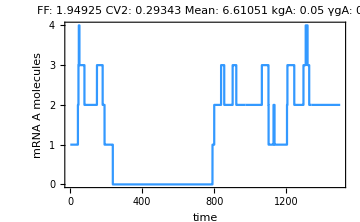
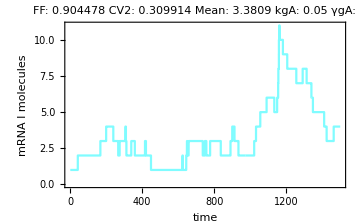
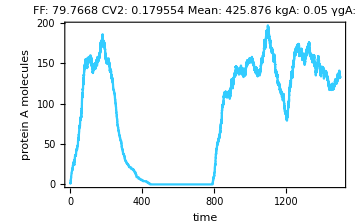
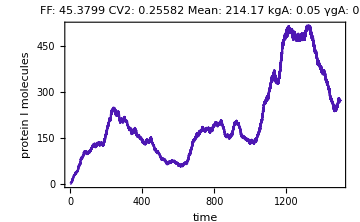
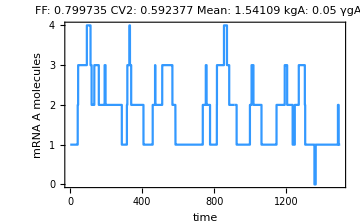
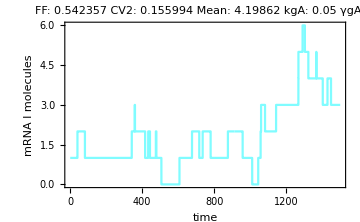
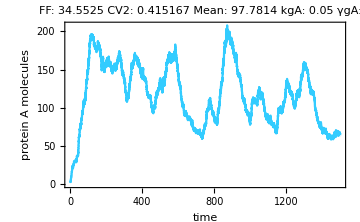
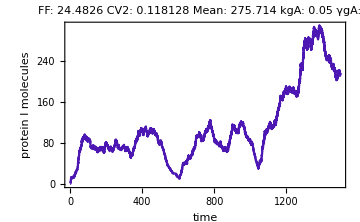
{{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{Null,Null},{Null,Null}},{{{DataStructure[OrderedHashSet, {Data -> {{0.517874, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.658335, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.05462, {1, 1, 1, 2, 1, 0, 1, 0}}, {1.18044, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.6947, {1, 3, 1, 2, 1, 0, 1, 0}}, {1.7476, {<<8>>}}, <<18976>>, {1499.46, {2, 133, 4, 274, 1, 0, 1, 0}}, {1499.46, {2, 133, 4, 273, 1, 0, 1, 0}}, {1499.58, {2, 133, 4, 272, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.108312, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.206263, {1, 2, 1, 2, 1, 0, 1, 0}}, {0.582462, {1, 2, 1, 3, 1, 0, 1, 0}}, {0.597961, {1, 3, 1, 3, 1, 0, 1, 0}}, {1.34563, {1, 4, 1, 3, 1, 0, 1, 0}}, {1.8092, {<<8>>}}, <<28393>>, {1499.41, {5, 156, 1, 80, 1, 0, 1, 0}}, {1499.44, {5, 157, 1, 80, 1, 0, 1, 0}}, {1499.52, {5, 157, 1, 79, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0994628, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.282764, {1, 2, 1, 2, 1, 0, 1, 0}}, {0.3239, {1, 2, 1, 3, 1, 0, 1, 0}}, {0.533672, {1, 2, 1, 4, 1, 0, 1, 0}}, {0.890712, {1, 3, 1, 4, 1, 0, 1, 0}}, {<<2>>}, <<34134>>, {1499.47, {10, 547, 3, 229, 1, 0, 1, 0}}, {1499.47, {10, 548, 3, 229, 1, 0, 1, 0}}, {1499.52, {10, 547, 3, 229, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0712227, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.930636, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.42096, {1, 3, 1, 2, 1, 0, 1, 0}}, {1.87669, {1, 4, 1, 2, 1, 0, 1, 0}}, {1.9086, {1, 5, 1, 2, 1, 0, 1, 0}}, {2.19851, <<1>>}, <<46911>>, {1499.44, {10, 781, 1, 92, 1, 0, 1, 0}}, {1499.48, {10, 782, 1, 92, 1, 0, 1, 0}}, {1499.56, {10, 782, 1, 93, 1, 0, 1, 0}}}}]},{DataStructure[OrderedHashSet, {Data -> {{0.152395, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.354198, {1, 3, 1, 1, 1, 0, 1, 0}}, {1.20314, {1, 3, 1, 2, 1, 0, 1, 0}}, {1.55957, {1, 3, 1, 3, 1, 0, 1, 0}}, {1.89876, {1, 4, 1, 3, 1, 0, 1, 0}}, {1.9032, {1, <<7>>}}, <<14959>>, {1499.32, {1, 64, 3, 214, 1, 0, 1, 0}}, {1499.39, {1, 64, 3, 213, 1, 0, 1, 0}}, {1499.55, {1, 64, 3, 214, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0640024, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.0946543, {1, 2, 1, 2, 1, 0, 1, 0}}, {0.21335, {1, 2, 1, 3, 1, 0, 1, 0}}, {0.313746, {1, 2, 1, 4, 1, 0, 1, 0}}, {0.425731, {1, 2, 1, 5, 1, 0, 1, 0}}, {0.478895, {<<8>>}}, <<21574>>, {1499.27, {0, 6, 2, 169, 1, 0, 1, 0}}, {1499.34, {0, 6, 2, 168, 1, 0, 1, 0}}, {1499.82, {0, 6, 2, 167, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.174803, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.538241, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.59189, {1, 3, 1, 2, 1, 0, 1, 0}}, {1.64445, {1, 4, 1, 2, 1, 0, 1, 0}}, {2.48542, {1, 4, 1, 3, 1, 0, 1, 0}}, {2.86278, <<1>>}, <<21633>>, {1499.42, {2, 170, 5, 295, 1, 0, 1, 0}}, {1499.45, {2, 170, 5, 296, 1, 0, 1, 0}}, {1499.56, {2, 170, 5, 297, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.00831805, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.0882666, {1, 2, 1, 2, 1, 0, 1, 0}}, {0.229931, {1, 3, 1, 2, 1, 0, 1, 0}}, {0.393349, {1, 4, 1, 2, 1, 0, 1, 0}}, {0.407004, {1, 4, 1, 3, 1, 0, 1, 0}}, {<<8>>, <<1>>}, <<26350>>, {1498.97, {0, 54, 3, 108, 1, 0, 1, 0}}, {1499.28, {0, 54, 3, 109, 1, 0, 1, 0}}, {1499.85, {0, 53, 3, 109, 1, 0, 1, 0}}}}]}},{{DataStructure[OrderedHashSet, {Data -> {{0.174929, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.858093, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.15581, {1, 3, 1, 2, 1, 0, 1, 0}}, {1.23471, {1, 3, 1, 3, 1, 0, 1, 0}}, {1.25232, {1, 4, 1, 3, 1, 0, 1, 0}}, {<<2>>}, <<113967>>, {1499.47, {41, 2606, 2, 164, 0, 1, 1, 0}}, {1499.48, {41, 2605, 2, 164, 0, 1, 1, 0}}, {1499.5, {41, 2606, 2, 164, 0, 1, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.00276195, {1, 1, 1, 2, 1, 0, 1, 0}}, {1.35471, {1, 1, 1, 3, 1, 0, 1, 0}}, {2.29869, {1, 2, 1, 3, 1, 0, 1, 0}}, {2.36958, {1, 2, 1, 4, 1, 0, 1, 0}}, {2.39295, {1, 2, 1, 5, 1, 0, 1, 0}}, {<<2>>}, <<141691>>, {1499.47, {39, 2374, 1, 79, 0, 1, 1, 0}}, {1499.49, {39, 2375, 1, 79, 0, 1, 1, 0}}, {1499.51, {39, 2374, 1, 79, 0, 1, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{1.7805, {1, 1, 1, 2, 1, 0, 1, 0}}, {2.24126, {1, 1, 1, 3, 1, 0, 1, 0}}, {3.33801, {1, 1, 1, 4, 1, 0, 1, 0}}, {3.52248, {1, 1, 1, 5, 1, 0, 1, 0}}, {3.74383, {1, 1, 1, 6, 1, 0, 1, 0}}, {<<7>>, <<1>>}, <<172750>>, {1499.48, {30, 2028, 2, 189, 1, 0, 1, 0}}, {1499.49, {30, 2029, 2, 189, 1, 0, 1, 0}}, {1499.5, {30, 2030, 2, 189, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.723149, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.794695, {1, 2, 1, 2, 1, 0, 1, 0}}, {0.992299, {1, 2, 1, 3, 1, 0, 1, 0}}, {1.01121, {1, 3, 1, 3, 1, 0, 1, 0}}, {1.13722, {1, 4, 1, 3, 1, 0, 1, 0}}, {<<2>>}, <<190522>>, {1499.49, {22, 1557, 3, 181, 1, 0, 1, 0}}, {1499.5, {22, 1558, 3, 181, 1, 0, 1, 0}}, {1499.51, {22, 1557, 3, 181, 1, 0, 1, 0}}}}]},{DataStructure[OrderedHashSet, {Data -> {{0.953089, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.984545, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.46813, {1, 2, 1, 3, 1, 0, 1, 0}}, {1.72127, {1, 2, 1, 4, 1, 0, 1, 0}}, {2.55534, {1, 2, 1, 5, 1, 0, 1, 0}}, {2.87799, {<<8>>}}, <<39446>>, {1499.24, {0, 240, 4, 227, 1, 0, 1, 0}}, {1499.4, {0, 240, 4, 228, 1, 0, 1, 0}}, {1499.72, {0, 240, 4, 229, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.570389, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.576925, {1, 3, 1, 1, 1, 0, 1, 0}}, {0.729922, {1, 4, 1, 1, 1, 0, 1, 0}}, {1.79044, {1, 4, 1, 2, 1, 0, 1, 0}}, {1.92843, {1, 5, 1, 2, 1, 0, 1, 0}}, {2.37654, <<1>>}, <<40991>>, {1499.48, {4, 299, 4, 325, 1, 0, 1, 0}}, {1499.49, {4, 299, 4, 324, 1, 0, 1, 0}}, {1499.56, {4, 300, 4, 324, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0244152, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.214381, {1, 3, 1, 1, 1, 0, 1, 0}}, {0.356444, {1, 4, 1, 1, 1, 0, 1, 0}}, {0.361124, {1, 4, 1, 2, 1, 0, 1, 0}}, {0.813177, {1, 5, 1, 2, 1, 0, 1, 0}}, {<<2>>}, <<49332>>, {1499.44, {2, 205, 4, 222, 1, 0, 1, 0}}, {1499.49, {2, 205, 4, 221, 1, 0, 1, 0}}, {1499.52, {2, 205, 4, 220, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.789584, {1, 1, 1, 2, 1, 0, 1, 0}}, {1.52451, {1, 1, 1, 3, 1, 0, 1, 0}}, {1.77748, {1, 1, 1, 4, 1, 0, 1, 0}}, {2.21732, {1, 2, 1, 4, 1, 0, 1, 0}}, {2.45866, {1, 2, 1, 5, 1, 0, 1, 0}}, {2.57748, {<<8>>}}, <<53118>>, {1499.44, {1, 116, 5, 413, 1, 0, 1, 0}}, {1499.49, {1, 116, 5, 412, 1, 0, 1, 0}}, {1499.72, {1, 116, 5, 411, 1, 0, 1, 0}}}}]}}}}

```mathematica
s
```

```mathematica
s=Flatten[Table[simu[iteraciones2,replicas2,h,kIA,kAA,kAI,kgA,γgA,kmA,γmA,kpA,γpA,kgI,γgI,kmI,γmI,kpI,γpI,rep,"\n kgA: " <>ToString[kgA]<>" γgA: "<>ToString[γgA](*parametros*),lagStep,species],{kgI,{0.05,1}},{γgI,{0.2,2}}],{3}];
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},Null,{DataStructure[OrderedHashSet, {Data -> {{0.437847, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.44613, {1, 3, 1, 1, 1, 0, 1, 0}}, {0.537985, {1, 3, 1, 2, 1, 0, 1, 0}}, {0.603531, {1, 3, 1, 3, 1, 0, 1, 0}}, {1.27977, {1, 4, 1, 3, 1, 0, 1, 0}}, {1.95511, {1, <<6>>, 0}}, <<13342>>, {1499.15, {0, 0, 1, 90, 1, 0, 1, 0}}, {1499.22, {0, 0, 1, 89, 1, 0, 1, 0}}, {1499.55, {0, 0, 1, 88, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0624876, {1, 1, 1, 2, 1, 0, 1, 0}}, {0.640338, {1, 2, 1, 2, 1, 0, 1, 0}}, {1.47385, {1, 3, 1, 2, 1, 0, 1, 0}}, {1.49416, {1, 3, 1, 3, 1, 0, 1, 0}}, {1.71852, {1, 4, 1, 3, 1, 0, 1, 0}}, {1.89764, <<1>>}, <<15239>>, {1499.47, {2, 118, 4, 216, 1, 0, 1, 0}}, {1499.48, {2, 119, 4, 216, 1, 0, 1, 0}}, {1499.53, {2, 119, 4, 217, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.388474, {1, 2, 1, 1, 1, 0, 1, 0}}, {0.823475, {1, 3, 1, 1, 1, 0, 1, 0}}, {1.2296, {1, 4, 1, 1, 1, 0, 1, 0}}, {1.6243, {1, 4, 1, 2, 1, 0, 1, 0}}, {2.45049, {1, 4, 1, 3, 1, 0, 1, 0}}, {3.31665, {1, <<7>>}}, <<18047>>, {1499.3, {1, 81, 3, 243, 1, 0, 1, 0}}, {1499.46, {1, 81, 3, 242, 1, 0, 1, 0}}, {1499.63, {1, 81, 3, 241, 1, 0, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.429898, {1, 1, 1, 2, 1, 0, 1, 0}}, {1.42874, {1, 1, 1, 3, 1, 0, 1, 0}}, {1.51222, {1, 1, 1, 4, 1, 0, 1, 0}}, {1.74311, {1, 2, 1, 4, 1, 0, 1, 0}}, {2.5508, {1, 2, 1, 5, 1, 0, 1, 0}}, {3.01864, {1, <<7>>}}, <<18104>>, {1499.29, {3, 67, 3, 232, 1, 0, 1, 0}}, {1499.37, {3, 66, 3, 232, 1, 0, 1, 0}}, {1499.51, {3, 66, 3, 231, 1, 0, 1, 0}}}}]}}